## PRAVILNI VEČKOTNIKI IN PLATONSKA TELESA

### Pravilni večkotniki

```mathematica
Narisi[p__PravilniNKotnik] := Graphics[{
	Line[
		Table[{p[[2]] * Cos[(2*Pi * i) / p[[1]]],
		p[[2]] * Sin[(2*Pi * i) / p[[1]]]}, {i, 0, p[[1]]}]]}]
Obseg[p__PravilniNKotnik] := p[[1]] * p[[2]]
```

#### Enakostranični trikotnik

```mathematica
VišinaTrikotnika[p__PravilniNKotnik] := 3^(1/2)/2 * p[[2]]
PloščinaTrikotnika[p__PravilniNKotnik] := VišinaTrikotnika[p]*p[[2]]/2
```

```mathematica
p3 = PravilniNKotnik[3, 2];
Obseg[p3]
V = VišinaTrikotnika[p3]
P = PloščinaTrikotnika[p3]
```

6

√3

√3

```mathematica
NarisiVisino[p__V] := Graphics[
	Line[{p[[2]], 0},
			p[[2]] * Sin[(2*Pi * i) / p[[1]]]
			]
			]
```

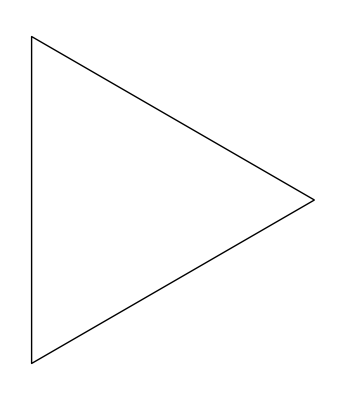

```mathematica
Narisi[p3]
```

#### Kvadrat

```mathematica
p4 = PravilniNKotnik[4, 2];
```

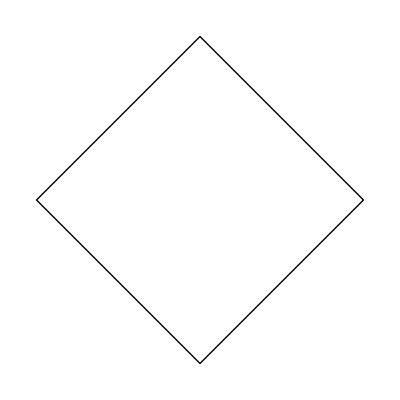

```mathematica
Narisi[p4]
```

#### Pravilni 5-kotnik

```mathematica
p5 = PravilniNKotnik[5, 2];
```

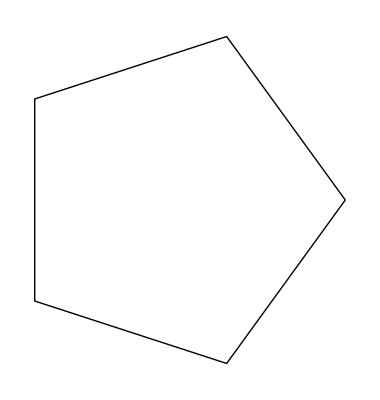

```mathematica
Narisi[p5]
```

#### Pravilni n-kotniki

```mathematica
d = 2;
Manipulate[Graphics[{
	Line[
		Table[{d * Cos[(2*Pi * i) / n],
		d * Sin[(2*Pi * i) / n]}, {i, 0, n}]]}], {n, 3, 20}]
```

#### Platonska telesa

Tetraeder

```mathematica
Graphics3D[Tetrahedron[{{1,0,0},{1,0,1},{1,1,1},{0,0,1}}]]
```

-Graphics3D-

Kocka

```mathematica
Graphics3D[Cuboid[]]
```

-Graphics3D-

Oktaeder

```mathematica
v={{-1, -1, 0}, {-1, 1, 0}, {0, 0, -(1/Sqrt[2])}, 
  {0, 0, 1/Sqrt[2]}, {1, -1, 0}, {1, 1, 0}};
Graphics3D[GraphicsComplex[v,
 Polygon[{{4, 5, 6}, {4,6, 2}, {4, 2, 1}, {4, 1, 5}, {5, 1, 3}, {5, 3, 6}, 
   {3, 1, 2}, {6, 3, 2}}]]]
```

-Graphics3D-

Ikozaeder

Dodekaeder